Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

1-7 Even and odd functions
Are the following functions even or odd or neither even nor odd?

1. ⅇ^x,ⅇ^(-|x|),x^3 cos nx, x^2 tan πx, sinh x -cosh x

```mathematica
ⅇ^2+ⅇ^-2
```

1/ⅇ^2+ⅇ^2

```mathematica
ⅇ^(Abs[-2])+ⅇ^(-Abs[-2])
```

1/ⅇ^2+ⅇ^2

```mathematica
x^2 Tan[π x]+x^2 Tan[-π x]
```

0

```mathematica
(Sinh[x]-Cosh[x])+(Sinh[-x]-Cosh[-x])
```

-2 Cosh[x]

1. So the list would run: neither, even, odd, odd, neither.

3.Even 5.Even

8 -17. Fourier series for period p=2L
Is the given function even or odd or neither even nor odd? Find its Fourier series.

9. Graphic stepwise function.

By inspection, it is odd.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Piecewise[{{-1, -2<x<0},{1,0<x<2}}]
```

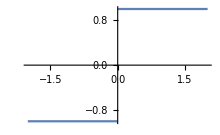

```mathematica
Plot[Piecewise[{{-1, -2<x<0},{1,0<x<2}}], {x,-2,2}]
```

```mathematica
FourierSeries[e1[x],x,5,FourierParameters->{1,π/2}]//ComplexExpand
```

(4 Sin[(π x)/2])/π+(4 Sin[(3 π x)/2])/(3 π)+(4 Sin[(5 π x)/2])/(5 π)

The function is odd. The period of the problem is p = 4, so L=2. Setting FourierParameters to correct values is necessary to get the text form of the answer, shown above. Helpful was https://classes.engineering.wustl.edu/jemt3170/Mathematica%20-%20Fourier%20Series.pdf.  If the period is already expressed in terms of factors of pi, then the second FourierParameter may be set to some integer. On the other hand, if the period (and integration limits) are in terms of non-pi rationals, as here, then the second FourierParameter probably needs some expression of pi in it. (It is interesting to note that if -π/2 instead of π/2is chosen as the second FourierParameter, exactly the same answer expression is produced.) I will set forth a rule for this sort of problem: the initial value of the second FourierParameter will be π, and that value will be adjusted by dividing by L.

11. f(x)=x^2  (-1<x<1), p = 2

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_] := x^2 (*/; -1<x<1*)
```

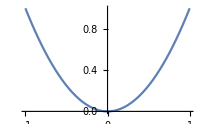

```mathematica
Plot[e1[x], {x,-1,1}]
```

```mathematica
FourierSeries[e1[x],x,3,FourierParameters->{1,π}]//ComplexExpand
```

1/3-(4 Cos[π x])/π^2+Cos[2 π x]/π^2-(4 Cos[3 π x])/(9 π^2)

The function is even.

The above answer matches the text. The problem states that p = 2, so L = 1.  The value of the second FourierParameter determined by the rule stated above is successfully used here.

13. The problem description is in the form of a plot.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Piecewise[{{0, -1/2<x<0},{x,0<x<1/2}}]
```

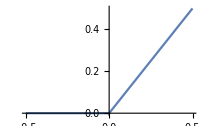

```mathematica
Plot[Piecewise[{{0, -1/2<x<0},{x,0<x<1/2}}], {x,-1/2,1/2}]
```

```mathematica
FourierSeries[e1[x],x,3,FourierParameters->{1,2π}]//ComplexExpand
```

1/8-Cos[2 π x]/π^2-Cos[6 π x]/(9 π^2)+Sin[2 π x]/(2 π)-Sin[4 π x]/(4 π)+Sin[6 π x]/(6 π)

The function is neither even nor odd. The period is 1, so that makes L = 1/2.  The above answer matches the text, and comprises the two series which make up the function. The choice of second FourierParameter agrees with the rule cited in the last note. The Mathematica command format for FourierSeries, calling as it does for a specific number of terms, does not allow the answer to express the unbounded nature of the series.

15. The problem description is in the form of a plot.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Piecewise[{{-x-π, -π<x<-π/2},{x,-π/2<x<π/2},{-x+π,π/2<x<π}}]
```

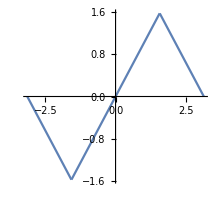

```mathematica
Plot[e1[x], {x,-π,π},AspectRatio->Automatic]
```

```mathematica
FourierSeries[e1[x],x,5, FourierParameters->{1,1}]//ComplexExpand
```

(4 Sin[x])/π-(4 Sin[3 x])/(9 π)+(4 Sin[5 x])/(25 π)

The function is odd.

The period is 2π, so that makes L = 1*π. The form of the answer shown above matches the text. Adjusting the second FourierParameter brings the parameter values to default values, so it would not be necessary to show them at all in this case.

17. The problem description is in the form of a plot.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Piecewise[{{x+1, -1<x<0},{-x+1,0<x<1}}]
```

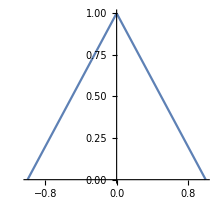

```mathematica
Plot[e1[x], {x,-1,1},AspectRatio->Automatic]
```

```mathematica
FourierSeries[e1[x],x,5, FourierParameters->{1,π}]//ComplexExpand
```

1/2+(4 Cos[π x])/π^2+(4 Cos[3 π x])/(9 π^2)+(4 Cos[5 π x])/(25 π^2)

The function is even.

The period is 2, so L =1. This makes the second FourierParameter equal π, according to the rule proposed previously. The resulting answer, above, matches the text.

19. Show that the familiar identities cos^3 x, sin^3 x, sin^4 x can be interpreted as Fourier series expansions. Develop cos^4 x.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Cos[x]^3
```

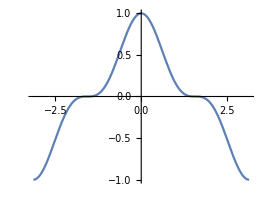

```mathematica
Plot[e1[x], {x,-π,π},AspectRatio->Automatic]
```

```mathematica
FourierSeries[e1[x],x,5, FourierParameters->{1,1}]//ComplexExpand
```

(3 Cos[x])/4+1/4 Cos[3 x]

The cos function is even. The period is 2π, so L = π. The form shown above agrees with text. The rule for second FourierParameter still works.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Sin[x]^3
```

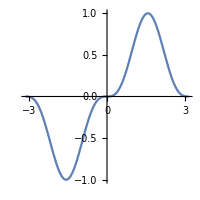

```mathematica
Plot[e1[x], {x,-π,π},AspectRatio->Automatic, ImageSize->200]
```

```mathematica
FourierSeries[e1[x],x,5, FourierParameters->{1,1}]//ComplexExpand
```

(3 Sin[x])/4-1/4 Sin[3 x]

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Cos[x]^4
```

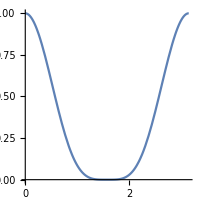

```mathematica
Plot[e1[x], {x,0,π},AspectRatio->Automatic, ImageSize->200]
```

```mathematica
FourierSeries[e1[x],x,5, FourierParameters->{1,2}]//ComplexExpand
```

3/8+1/2 Cos[2 x]+1/8 Cos[4 x]

The sin^4 function is even. The period is π, and L=π/2. This is the cause for assigning the second FourierParameter as shown above. The expected development of the function is not shown in the text, so agreement can’t be checked.

23 -29 Half-Range Expansions
Find (a) the Fourier cosine series, (b) the Fourier sine series. Sketch f(x) and its two periodic extensions.

23. The problem is described in a graphic sketch.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Piecewise[{{1, 0<x<4}}]
```

```mathematica
Plot[e1[x], {x,0,4},AspectRatio->Automatic, ImageSize->120]
```

-Graphics-

```mathematica
FourierSinSeries[e1[x],x,5, FourierParameters->{1,π/4}]//ComplexExpand
```

(4 Sin[(π x)/4])/π+(4 Sin[(3 π x)/4])/(3 π)+(4 Sin[(5 π x)/4])/(5 π)

```mathematica
FourierCosSeries[e1[x],x,5, FourierParameters->{1,π/4}]//ComplexExpand
```

1

There is no clue as whether the function is even or odd. The answer states that L=4. Assigning the second FourierParameter accordingly, the text answers are obtained for sin and cos.

25. The problem is shown in a sketch.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Piecewise[{{π-x, 0<x<π}}]
```

```mathematica
Plot[e1[x], {x,0,π},AspectRatio->Automatic, ImageSize->130]
```

-Graphics-

```mathematica
FourierCosSeries[e1[x],x,5, FourierParameters->{1,1}]//ComplexExpand
```

π/2+(4 Cos[x])/π+(4 Cos[3 x])/(9 π)+(4 Cos[5 x])/(25 π)

```mathematica
FourierSinSeries[e1[x],x,5, FourierParameters->{1,1}]//ComplexExpand
```

2 Sin[x]+Sin[2 x]+2/3 Sin[3 x]+1/2 Sin[4 x]+2/5 Sin[5 x]

Using the experience of the last problem, L is assumed to be π. This assumption produces the text result.

27. The problem is shown in a sketch.

```mathematica
Clear["Global`*"]
```

```mathematica
e1[x_]:=Piecewise[{{π/2, 0<x<π/2},{π-x, π/2<x<π}}]
```

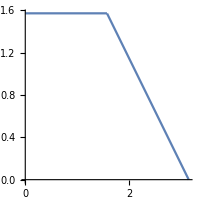

```mathematica
Plot[e1[x], {x,0,π},AspectRatio->Automatic, ImageSize->200]
```

```mathematica
FourierCosSeries[e1[x],x,5, FourierParameters->{1,1}]//ComplexExpand
```

(3 π)/8+(2 Cos[x])/π-Cos[2 x]/π+(2 Cos[3 x])/(9 π)+(2 Cos[5 x])/(25 π)

```mathematica
FourierSinSeries[e1[x],x,5, FourierParameters->{1,1}]//ComplexExpand
```

Sin[x]+(2 Sin[x])/π+1/2 Sin[2 x]+1/3 Sin[3 x]-(2 Sin[3 x])/(9 π)+1/4 Sin[4 x]+1/5 Sin[5 x]+(2 Sin[5 x])/(25 π)

Here again, L is assumed to be π. The text answers are obtained.

29. f(x)=sin x, with (0<x<π)

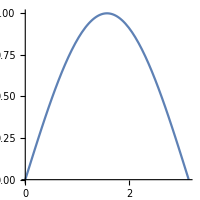

```mathematica
Clear["Global`*"]
e1[x_]:= Sin[x] 

Plot[e1[x], {x,0,π},AspectRatio->Automatic, ImageSize->200]
```

```mathematica
FourierCosSeries[e1[x],x,6, FourierParameters->{1,1}]//ComplexExpand
```

2/π-(4 Cos[2 x])/(3 π)-(4 Cos[4 x])/(15 π)-(4 Cos[6 x])/(35 π)

```mathematica
FourierSinSeries[e1[x],x,5, FourierParameters->{1,1}]//ComplexExpand
```

Sin[x]

The above answer for FourierSinSeries matches the text, but the above answer for FourierCosSeries does not match the text. The text answer has as arguments cos x, cos 3x, cos 5x etc., as:

2/π-(4 Cos[ x])/(3 π)-(4 Cos[3 x])/(15 π)-(4 Cos[5 x])/(35 π)
not the even numbered x-arguments. However, https://web.mit.edu/jorloff/www/18.03-esg/notes/topic23.pdf, p.7 contradicts this answer, and supports the even-x pattern above. With its detailed development of the topic, I’m inclined to go with the external source.